## The pattern in modern English.

### Morphological Relation System

What is this, over the time, human language evolve by "morph". I am not professional in linguistic, but any one using English will know the something similar between group of words, like “dependent,independent,...”

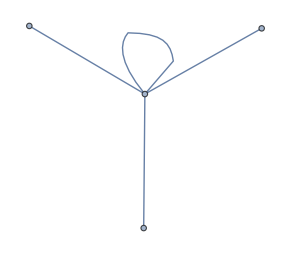

```mathematica
Thread[#->WordData[#,"MorphologicalDerivatives","List"]]& @"love"//GraphPlot
```

```mathematica
dicWords=DictionaryLookup[];
```

```mathematica
wordDerivativeToSystem = ParallelMap[Thread[#->WordData[#,"MorphologicalDerivatives","List"]]&,dicWords]//DeleteCases[#,_Missing]&//Select[#,ListQ@Values@#&& Length@# != 0 &]& //Flatten //Select[#,StringQ @ Keys @# && StringQ@Values@#&]&
```

```mathematica
wordDerivativeFromSystem = ParallelMap[Thread[#->WordData[#,"MorphologicalSource","List"]]&,dicWords]//DeleteCases[#,_Missing]&//Select[#,ListQ@Values@#&& Length@# != 0 &]& //Flatten//Select[#,StringQ @ Keys @# && StringQ@Values@#&]&
```

```mathematica
graphMorp = (UndirectedEdge[Keys@#,Values@#]&/@ ({(wordDerivativeToSystem),wordDerivativeFromSystem}//Flatten )//Union)//Graph[#,VertexLabels->Automatic]&
```

```mathematica
componentWordMorp = graphMorp// WeaklyConnectedComponents //Select[#,Length@#>1&]&
```

```mathematica
componentGraphWordMorp = graphMorp// WeaklyConnectedGraphComponents;
```

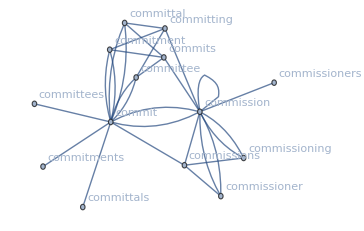

```mathematica
componentGraphWordMorp[[50]]
```

Surprise, around 100000 dictionary English word, if group them based on they Morphology, we have only 10000 groups. Some group easy to understand, but some groups, like

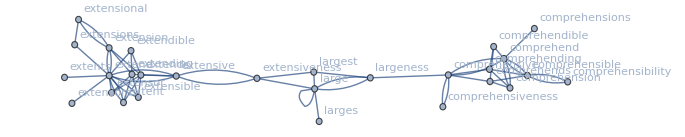

```mathematica
componentGraphWordMorp[[1]]
```

A bit hard to understand, why “large” derivative related from extensive group and “comprehensive”

```mathematica
WordData["extensiveness","MorphologicalDerivatives","List"]
```

{extensive,large}

```mathematica
WordData["largest","MorphologicalSource","List"]
```

{extensiveness,large,largeness}

```mathematica
DictionaryLookup[RegularExpression[".*larg.*"]]
```

{enlarge,enlargeable,enlarged,enlargement,enlargements,enlarger,enlargers,enlarges,enlarging,large,largehearted,largely,largeness,larger,larges,largess,largest,largish,largo,largos,overlarge}

```mathematica
Select[componentWordMorp,Length@((StringPosition[#,"larg"]//Flatten))> 0 &]
```

{{extensiveness,extensive,large,largest,extend,extending,extends,largeness,larges,extendible,extensible,extension,extensor,extent,extensions,extensors,extents,comprehensive,extensional,comprehend,comprehending,comprehends,comprehensiveness,comprehendible,comprehensible,comprehension,comprehensions,comprehensibility},{enlarging,enlargement,enlarger,enlarge,enlarges,enlargements,enlargers},{largo,largos}}

Surprisingly,  “largo” and “large” in different group. Despite of  similar in written form

```mathematica
#->Column [ Text/@WordData[#,"Definitions","List"],Frame->All]&/@ {"largo","large"}
```

{largo→(music) a composition or passage that is to be performed in a slow and dignified manner
very slow in tempo and broad in manner
slowly and broadly,large→a garment size for a large person
in an advanced stage of pregnancy
having broad power and range and scope
conspicuous in position or importance
generous and understanding and tolerant
above average in size or number or quantity or magnitude or extent
ostentatiously lofty in style
fairly large or important in effect; influential
in a boastful manner
with the wind abaft the beam
at a distance, wide of something (as of a mark)}

```mathematica
Select[componentWordMorp,Length@((StringPosition[#,"depen"]//Flatten))> 0 &]
```

{{dependant,depend,depended,depending,depends,dependency,dependent,dependencies,dependence,dependents},{interdepend,interdependence,interdependency,interdependent},{undependableness,undependable,undependability},{dependability,dependable,dependableness},{independence,independent,independency}}

```mathematica
WordData[#,"MorphologicalDerivatives","List"]&/@{"independence","independent","independency"}
```

{{independent},{independence,independency},{independent}}

### How about split groups of words based on Synonyms

```mathematica
wordSynonymsSystem = ParallelMap[Thread[#->WordData[#,"Synonyms","List"]]&,dicWords]//DeleteCases[#,_Missing]&//Select[#,ListQ@Values@#&& Length@# != 0 &]& //Flatten //Select[#,StringQ @ Keys @# && StringQ@Values@#&]&
```

```mathematica
wordSynonymsSystemGraph = (Sort /@(UndirectedEdge[#[[1]],#[[2]]] &/@ wordSynonymsSystem ))//DeleteDuplicates//Graph
```

```mathematica
synonymsCluster = wordSynonymsSystemGraph// ConnectedComponents;
```

```mathematica
synonymsCluster//Length
```

16147

Oh, we have 16000 clusters here

```mathematica
synonymsClusterGraph = wordSynonymsSystemGraph//ConnectedGraphComponents;
```

```mathematica
VertexCount /@ synonymsClusterGraph
```

Wow, the biggest cluster, why it is so huge

```mathematica
adjMatrix = synonymsClusterGraph[[1]]//AdjacencyMatrix
```

SparseArray[<370990>, {43071, 43071}]

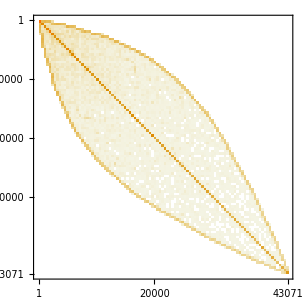

```mathematica
MatrixPlot[adjMatrix]
```

```mathematica
synonymsClusterGraph[[1]]//VertexDegree//Counts // KeySort
```

<|1→2208,2→6270,3→4677,4→4639,5→3560,6→3229,7→2565,8→2198,9→1789,10→1441,11→1242,12→1221,13→858,14→766,15→634,16→585,17→507,18→446,19→378,20→369,21→286,22→245,23→241,24→217,25→184,26→181,27→134,28→180,29→123,30→123,31→118,32→112,33→83,34→84,35→71,36→62,37→71,38→51,39→47,40→59,41→59,42→64,43→38,44→26,45→41,46→54,47→37,48→32,49→35,50→27,51→30,52→16,53→25,54→19,55→15,56→25,57→20,58→12,59→20,60→8,61→10,62→15,63→15,64→8,65→12,66→11,67→4,68→8,69→8,70→8,71→2,72→10,73→1,74→6,75→7,77→7,78→3,80→1,81→4,82→3,83→3,84→4,85→4,87→6,88→1,89→1,91→1,92→4,94→1,95→1,96→2,97→1,98→2,99→3,100→4,101→1,102→3,103→3,104→1,106→1,107→1,109→1,111→1,114→1,115→2,119→1,120→1,123→1,127→1,129→1,134→1,137→2,143→1,144→1,146→1,155→1,156→1,169→1,175→1,182→1,190→1,201→1|>

Wait, just a quick skim through this small vertex degree list, there is a word that have ... 201 synonyms, or I mean the vertex of this word have 201 edges connect with it! What the hell is that word. There are many word have hundreds synonyms too!.

```mathematica
synonymsClusterGraph[[1]]//VertexDegree//Position[#,201]&
```

{{663}}

```mathematica
(synonymsClusterGraph[[1]]//VertexList)[[663]]
```

break

```mathematica
VertexDegree[synonymsClusterGraph[[1]],"break"]
```

201

```mathematica
WordData["break","Synonyms","List"]
```

{bankrupt,better,breach,breakage,break away,break-dance,break dance,break down,break in,breaking,break off,break of serve,break out,breakout,break up,bring out,bump,burst,bust,cave in,check,collapse,come apart,conk out,crack,damp,dampen,demote,develop,die,disclose,discontinue,discover,disruption,divulge,erupt,expose,fail,fall apart,fall in,falling out,fault,faulting,founder,fracture,gaolbreak,gap,geological fault,get around,get out,give,give away,give out,give way,go,go against,go bad,good luck,happy chance,infract,intermission,intermit,interrupt,interruption,jailbreak,kick downstairs,let on,let out,offend,open frame,part,pause,prisonbreak,prison-breaking,recess,recrudesce,relegate,respite,reveal,rift,ruin,rupture,separate,severance,shift,smash,snap off,soften,split,split up,stop,suspension,time out,transgress,unwrap,violate,weaken,wear,wear out}

```mathematica
synonymsOfBreak = Select[synonymsClusterGraph[[1]]//EdgeList,#[[1]]=="break"|| #[[2]]== "break"&];
```

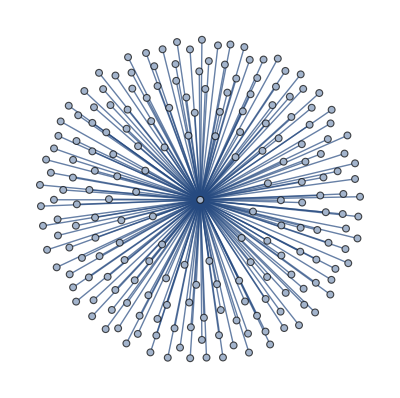

```mathematica
synonymsOfBreak//Graph
```

```mathematica
synonymsOfBreak//Shallow
```

{break<->bump,break<->check,break<->go,break<->stop,break<->bumped,break<->bumping,break<->bumps,break<->checking,break<->checks,break<->breaks,«191»}

Huh? what is relation of break and bump

```mathematica
WordData["bump","Synonyms"]
```

{{bump,Noun,Impact}→{blow},{bump,Noun,Projection}→{bulge,excrescence,extrusion,gibbosity,gibbousness,hump,jut,prominence,protrusion,protuberance,swelling},{bump,Noun,Hurt}→{},{bump,Verb,RunInto}→{knock},{bump,Verb,Displace}→{dislodge},{bump,Verb,TripTheLightFantasticToe}→{},{bump,Verb,Happen}→{chance,encounter,find,happen},{bump,Verb,Designate}→{break,demote,kick downstairs,relegate}}

Oh! the problem that in “designate” sense form of bump, there is a link to “break”, “break” someone is meaning demote someone. Our algorithm work, but maybe it just so general, or the data so rich that why everything keep link instead of separate themself.

Let try to minimize our examine set to Noun only

```mathematica
nounWords = WordList["Noun"];
```

```mathematica
nounSynonymsSystem = ParallelMap[Thread[#->WordData[{#,"Noun"},"Synonyms","List"]]&,nounWords]//DeleteCases[#,_Missing]&//Select[#,ListQ@Values@#&& Length@# != 0 &]& //Flatten //Select[#,StringQ @ Keys @# && StringQ@Values@#&]&
```

```mathematica
nounSynonymsSystemGraph = (Sort /@ (#[[1]] <->#[[2]]&/@ nounSynonymsSystem))//DeleteDuplicates//Graph[#,VertexLabels->Automatic]&
```

```mathematica
nounSynonymsSystemGraphComponent = nounSynonymsSystemGraph//ConnectedComponents;
```

```mathematica
Length /@ nounSynonymsSystemGraphComponent //Shallow
```

{11689,37,35,32,31,29,27,27,27,27,«6465»}

Oops, understand, English simply so rich at the senses of each words and even each senses have multi synonyms too.

```mathematica
graphsSystem2 = nounSynonymsSystemGraph//ConnectedGraphComponents;
```

If we ignore the exceptional huge cluster, let check remain cluster

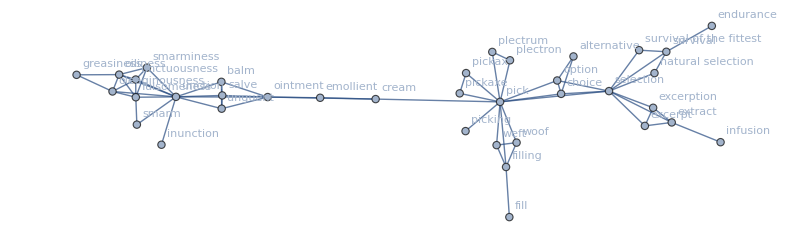

```mathematica
graphsSystem2[[2]]
```

Hum, I don' t know fill can act like a noun

```mathematica
Column[#,Frame->All]&@ (Text/@WordData[{"fill","Noun"},"Definitions"])
```

{fill,Noun,Sufficiency}→a quantity sufficient to satisfy
{fill,Noun,Stuff}→any material that fills a space or container

Oh, the “magic” of English, how on Earth "fill" which act like a noun existed. but it really existed.

Normally I never expect a word that have so many synonyms, but in the end most of us just touch a very basic of English skill in our era. a simple and common like “break”. If count all of its “sense”, can have up to 200 synonyms, such a massive amount of knowledge if we dig into it

## Scratchpad

```mathematica
SetDirectory["~/nhannht-projects/nature"];
```

```mathematica
NotebookSave[EvaluationNotebook[],FileNameJoin[{Directory[],"humanlanguage2.nb"}]]
```

```mathematica
VerminExportKeepSyntaxHighLight[]
```

```mathematica
Export[FileNameJoin[{Directory[],"humanlanguage2.pdf"}],EvaluationNotebook[]]
```

/home/vermin/nhannht-projects/nature/humanlanguage2.pdf